This script is a part of ANGEL project.
V 1.3
2018.02.07
(C) Vulpes Corsac

```mathematica
Clear["Global`*"];(* Clearing all variables *)
Needs["JLink`"];(* Not to be any problems with exporting *)
ReinstallJava[JVMArguments -> "-Xmx512m"];(* DO NOT TOUCH! *)
```

```mathematica
Kprt=-6.; (* K^prt for current resonance *)
```

```mathematica
importDir = "ImportData";(* Directory for importing data *)
exportDir = "ExportData";(* Directory for exporting data *)
```

```mathematica
phaseColumnName="Theta"; (* Name of column in data file with phase *)
phaseSDColumnName="ThetaSD"; (* Name of column in data file with phase *)
frequencyColumnName="Fext";(* Name of column in data file with frequency *)
timeColumnName="Time";(* Name of column in data file with time *)
```

```mathematica
lorenz[y0_,A_,μ_, σ_, x_]:=y0 + (2A)/π×σ/(4 (x-μ)^2+σ^2);(* Lorenz function *)
lorenzInverse[y0_,A_,μ_, σ_, y_,sgn_]:=Sign[sgn]×√((2 A σ)/(4 π (y-y0))-σ^2/4)+μ;(* Inverse Lorenz function *)
paraboloid[y0_,A_,μ_,x_] := y0 + A(x-μ)^2;(* Paraboloid *)
```

```mathematica
Experiments = Length[FileNames["PreScan*.dat",FileNameJoin[{NotebookDirectory[ ],importDir}]]]; (* Getting experiments ammount *)
(* Preparing tables for plotting and exporting *)
TemperatureLorenzKineticsPlotRaw=Table[{i},{i,1,Experiments}];
TemperatureLorenzKineticsPlotAFix=Table[{i},{i,1,Experiments}];
TemperatureLorenzKineticsPlotY0Fix=Table[{i},{i,1,Experiments}];
TemperatureLorenzKineticsExport=Table[{i},{i,1,Experiments}];
TemperatureLorenzKineticsPlotAllFixDelta=Table[{i},{i,1,Experiments}];
```

```mathematica
For[i=1,i≤ Experiments,i=i+1,(* For all experiments *)
PreScanData=Import[FileNameJoin[{NotebookDirectory[ ],importDir,"PreScan"<>ToString[i]<>".dat"}]][[2;;]];(* Importing rezonance profile *)
PreScanFrequency=PreScanData[[All,1]];(* Getting frequency column *)
PreScanTheta=PreScanData[[All,6]];(* Getting phase column *)
PreScanData=Transpose[{PreScanFrequency,PreScanTheta}];(* Forming prescan data *)
PreScanLorenzFit=NonlinearModelFit[(* Fitting prescan data with lorenz *)
PreScanData,lorenz[y0,A,μ, σ,x],
{{y0,Max[PreScanTheta]},
{A,Min[PreScanTheta]-Max[PreScanTheta]},
{μ,PreScanFrequency[[Position[PreScanTheta,Min[PreScanTheta]][[1,1]]]]},
{σ,10}},
x];
parametersTablePreScanLorenzFit=PreScanLorenzFit["ParameterTable"];(* Getting fited parameters and their errors *)
y0LorenzFit=parametersTablePreScanLorenzFit[[1,1,2,2]];δy0LorenzFit=parametersTablePreScanLorenzFit[[1,1,2,3]];
ALorenzFit=parametersTablePreScanLorenzFit[[1,1,3,2]];δALorenzFit=parametersTablePreScanLorenzFit[[1,1,3,3]];
μLorenzFit=parametersTablePreScanLorenzFit[[1,1,4,2]];δμLorenzFit=parametersTablePreScanLorenzFit[[1,1,4,3]];
σLorenzFit=parametersTablePreScanLorenzFit[[1,1,5,2]];δσLorenzFit=parametersTablePreScanLorenzFit[[1,1,5,3]];
PreScanFitPlot=Show[(* Plotting round data and fittings *)
ListPlot[PreScanData,PlotLabel->"Phase fitting: Lorenz(Red)",AxesLabel->{"Frequency[Hz]","Phase[Deg]"},PlotRange->All],
Plot[lorenz[y0LorenzFit,ALorenzFit,μLorenzFit, σLorenzFit,x],{x,Min[PreScanFrequency],Max[PreScanFrequency]},ColorFunction->Function[{x,y},Red],PlotRange->All]
];
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"Data"<>ToString[i]<>"_Fit.png"}],PreScanFitPlot];(* Exporting plot from above *)
KineticsData=Import[FileNameJoin[{NotebookDirectory[ ],importDir,"Kinetics"<>ToString[i]<>".dat"}]][[2;;]];(* Importing kinetics data *)
KineticsTime=KineticsData[[All,12]];(* Getting time column *)
KineticsTheta=KineticsData[[All,6]];(* Getting phase column *)
KineticsData=Transpose[{KineticsTime,KineticsTheta}];(* Forming kinetics data *)
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"KineticsData"<>ToString[i]<>"_Raw.png"}],
ListPlot[KineticsData,PlotLabel->"Kinetics Data "<>ToString[i],AxesLabel->{"Time[s]","Phase[deg]"},ImageSize->Medium,PlotRange->All]];(* Just to be shure everything goes well *)
TimeMinTheta=KineticsTime[[Position[KineticsTheta,Min[KineticsTheta]][[1,1]]]];(* Finding phase minimum *)
(* Changing parameters for better fitting *)
ALorenzFitFix=1/2 π (Min[KineticsTheta]-y0LorenzFit) σLorenzFit;
y0LorenzFitFix=Min[KineticsTheta]-(2 ALorenzFit)/(π σLorenzFit);
parametersString="Lorenz fitting ( y0 + 2A/Pi * σ/(4 (x-μ)^2+σ^2) ):"<>"\n\t"<>(* Forming a string with fited parameters and their errors *)
"y0 = "<>ToString[y0LorenzFit]<>" ± "<>ToString[δy0LorenzFit]<>", t.m. "<>ToString[100×Abs[δy0LorenzFit/y0LorenzFit]]<>" %"<>"\n\t"<>
"A = "<>ToString[ALorenzFit]<>" ± "<>ToString[δALorenzFit]<>", t.m. "<>ToString[100×Abs[δALorenzFit/ALorenzFit]]<>" %"<>"\n\t"<>
"μ/10^3 = "<>ToString[μLorenzFit/10^3]<>" ± "<>ToString[δμLorenzFit]<>", t.m. "<>ToString[100×Abs[δμLorenzFit/μLorenzFit]×10^3]<>"×10^(-3) %"<>"\n\t"<>
"σ = "<>ToString[σLorenzFit]<>" ± "<>ToString[δσLorenzFit]<>", t.m. "<>ToString[100×Abs[δσLorenzFit/σLorenzFit]]<>" %"<>"\n"<>
"y0Fix = "<>ToString[y0LorenzFitFix]<>"\n"<>"AFix = "<>ToString[ALorenzFitFix]<>"\n";
;
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"Data"<>ToString[i]<>"_Fit.txt"}],parametersString];(* Exporting string from above *)
(* Forming data for kinetics fit *)
TemperatureLorenzFromTimeRaw=Table[{KineticsTime[[i]],lorenzInverse[y0LorenzFit,ALorenzFit,μLorenzFit, σLorenzFit,KineticsTheta[[i]],-KineticsTime[[i]]+TimeMinTheta]},
{i,1,Length[KineticsTime]}];
TemperatureLorenzFromTimeAFix=Table[{KineticsTime[[i]],lorenzInverse[y0LorenzFit,ALorenzFitFix,μLorenzFit, σLorenzFit,KineticsTheta[[i]],-KineticsTime[[i]]+TimeMinTheta]},
{i,1,Length[KineticsTime]}];
TemperatureLorenzFromTimeY0Fix=Table[{KineticsTime[[i]],lorenzInverse[y0LorenzFitFix,ALorenzFit,μLorenzFit, σLorenzFit,KineticsTheta[[i]],-KineticsTime[[i]]+TimeMinTheta]},
{i,1,Length[KineticsTime]}];
(* Frequency -> ΔTemperature *)
TemperatureLorenzFromTimeRaw[[All,2]]=(TemperatureLorenzFromTimeRaw[[All,2]]-TemperatureLorenzFromTimeRaw[[1,2]])/Kprt;
TemperatureLorenzFromTimeAFix[[All,2]]=1/Kprt(TemperatureLorenzFromTimeAFix[[All,2]]-TemperatureLorenzFromTimeAFix[[1,2]]);
TemperatureLorenzFromTimeY0Fix[[All,2]]=1/Kprt(TemperatureLorenzFromTimeY0Fix[[All,2]]-TemperatureLorenzFromTimeY0Fix[[1,2]]);
(* Forming data for plotting and exporting *)
TemperatureLorenzKineticsPlotRaw[[i]]=TemperatureLorenzFromTimeRaw;
TemperatureLorenzKineticsPlotAFix[[i]]=TemperatureLorenzFromTimeAFix;
TemperatureLorenzKineticsPlotY0Fix[[i]]=TemperatureLorenzFromTimeY0Fix;
TemperatureLorenzKineticsPlotAllFixDelta[[i]]=Transpose[{1/2(TemperatureLorenzFromTimeAFix[[All,1]]+TemperatureLorenzFromTimeY0Fix[[All,1]]),TemperatureLorenzFromTimeAFix[[All,2]]-TemperatureLorenzFromTimeY0Fix[[All,2]]}];
TemperatureLorenzKineticsExport[[i]]=Prepend[Transpose[Join[Transpose[TemperatureLorenzFromTimeRaw],Transpose[TemperatureLorenzFromTimeAFix],Transpose[TemperatureLorenzFromTimeY0Fix]]],{"Time[s] Lorenz "<>ToString[i]<>", Raw","ΔTemperature[C], Raw","Time[s] Lorenz "<>ToString[i]<>", Afix","ΔTemperature[C], Afix","Time[s] Lorenz "<>ToString[i]<>", Y0fix","ΔTemperature[C], y0Fix"}];
(* Plotting round kinetics data *)
TemperatureLorenzKineticsPlotRound= ListPlot[Evaluate[{TemperatureLorenzFromTimeRaw,TemperatureLorenzFromTimeAFix,TemperatureLorenzFromTimeY0Fix}],
PlotLabel->"Lorenz Raw(Blue), AFix(Orange), \nY0Fix(Green) phase fitting for round "<>ToString[i],AxesLabel->{"Time[s]","ΔTemperature[C]"},ImageSize->Medium,PlotRange->All];
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"KineticsRound"<>ToString[i]<>".png"}],TemperatureLorenzKineticsPlotRound];(* Exporting plot from above *)
];
```

```mathematica
(* Exporting calculated data *)
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"LorenzKinetics"<>".xlsx"}],TemperatureLorenzKineticsExport];
```

```mathematica
(* Getting plots for kinetics and exporting them *)
TemperatureLorenzKineticsPlotAllRaw= ListPlot[TemperatureLorenzKineticsPlotRaw,PlotLabel->"Lorenz phase fitting Raw",AxesLabel->{"Time[s]","ΔTemperature[C]"},ImageSize->Medium,PlotRange->All];
TemperatureLorenzKineticsPlotAllAFix= ListPlot[TemperatureLorenzKineticsPlotAFix,PlotLabel->"Lorenz phase fitting AFix",AxesLabel->{"Time[s]","ΔTemperature[C]"},ImageSize->Medium,PlotRange->All];
TemperatureLorenzKineticsPlotAllY0Fix= ListPlot[TemperatureLorenzKineticsPlotY0Fix,PlotLabel->"Lorenz phase fitting Y0Fix",AxesLabel->{"Time[s]","ΔTemperature[C]"},ImageSize->Medium,PlotRange->All];
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"LorenzKineticsRaw"<>".png"}],TemperatureLorenzKineticsPlotAllRaw];
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"LorenzKineticsAFix"<>".png"}],TemperatureLorenzKineticsPlotAllAFix];
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"LorenzKineticsY0Fix"<>".png"}],TemperatureLorenzKineticsPlotAllY0Fix];
```

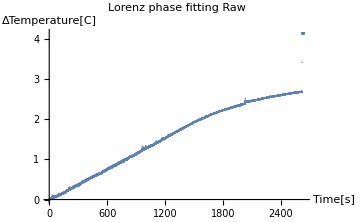
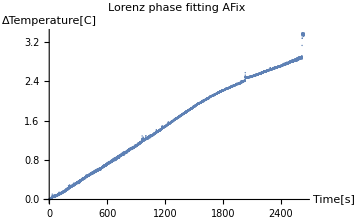
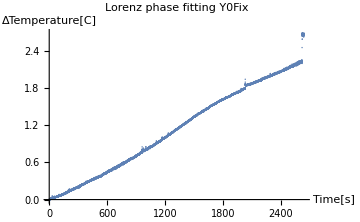

```mathematica
{TemperatureLorenzKineticsPlotAllRaw,TemperatureLorenzKineticsPlotAllAFix,TemperatureLorenzKineticsPlotAllY0Fix}(* Showing plots from above *)
```

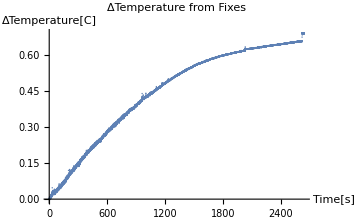

```mathematica
TemperatureLorenzKineticsPlotAllFixDeltaPlot= ListPlot[TemperatureLorenzKineticsPlotAllFixDelta,PlotLabel->"ΔTemperature from Fixes",AxesLabel->{"Time[s]","ΔTemperature[C]"},ImageSize->Medium,PlotRange->All]
Export[FileNameJoin[{NotebookDirectory[ ],exportDir,"LorenzKineticsFixesDelta"<>".png"}],TemperatureLorenzKineticsPlotAllFixDeltaPlot];
```

```mathematica
{{Afix=Solve[lorenz[y0,A,μ,σ,μ]==n,A][[1,1]],lorenz[y0,A/.Afix,μ,σ,μ]},
{y0Fix=FullSimplify[Solve[lorenz[y0,A,μ,σ,μ]==n,y0][[1,1]]],FullSimplify[lorenz[y0/.y0Fix,A,μ,σ,μ]]}}
```

{{A→1/2 π (n-y0) σ,n},{y0→n-(2 A)/(π σ),n}}